## Setup

NB!! Depending on whether we have inversion symmetry or not, where to put s changes

```mathematica
inversionSymmBroken = False;
If[inversionSymmBroken, tzsub=tz->tz, tzsub = tz->s tz] ;
```

```mathematica
ϵ[m_]:=If[m!=0,  tz kappa +Sign[m] α Sqrt[α Abs[m] + kappa^2],( tz- s α) kappa]/.α->1/.tzsub (* Keep α in the formula for later *)
```

```mathematica
alpha[m_]:=-Sqrt[Abs[m]]/((ϵ[m]- (tz/.tzsub) kappa)s- kappa)
```

```mathematica
xi=2*(HeavisideTheta[-ϵ[m]]-HeavisideTheta[-ϵ[n]])/((ϵ[m]-ϵ[n]+I η)^2 * (alpha[m]^2+1) *(alpha[n]^2+1));
```

```mathematica
stepRule:=HeavisideTheta[-ϵ[m_]]-HeavisideTheta[-ϵ[n_]]->Switch[m n > 0, True, 0, False, Switch[{m==0, n==0},
{True, True}, 0,
{False, False}, Sign[n],
{True, False}, Sign[n]HeavisideTheta[Sign[n] s kappa],
{False, True}, -Sign[m]HeavisideTheta[Sign[m] s kappa]
]] (* Assumes Type-I *)
```

NOTE : have to find out if the s before 2 kappa tz should be there

```mathematica
firstTerm[i_] =(ϵ[m] + ϵ[n]- 0 2kappa (tz/.tzsub))alpha[i]^2 Switch[i, n, 1, m, -1]
```

(Abs[i] (If[m≠0,(s tz) kappa+Sign[m] √(1 Abs[m]+kappa^2),(s tz-s 1) kappa]+If[n≠0,(s tz) kappa+Sign[n] √(1 Abs[n]+kappa^2),(s tz-s 1) kappa]) Switch[i,n,1,m,-1])/(-kappa+s (-kappa s tz+If[i≠0,(s tz) kappa+Sign[i] √(1 Abs[i]+kappa^2),(s tz-s 1) kappa]))^2

```mathematica
secondTerm=Sqrt[Abs[n]]alpha[n] +Sqrt[Abs[n]-1]alpha[m]alpha[n]^2
```

-((√Abs[m] √(-1+Abs[n]) Abs[n])/((-kappa+s (-kappa s tz+If[m≠0,(s tz) kappa+Sign[m] √(1 Abs[m]+kappa^2),(s tz-s 1) kappa])) (-kappa+s (-kappa s tz+If[n≠0,(s tz) kappa+Sign[n] √(1 Abs[n]+kappa^2),(s tz-s 1) kappa]))^2))-Abs[n]/(-kappa+s (-kappa s tz+If[n≠0,(s tz) kappa+Sign[n] √(1 Abs[n]+kappa^2),(s tz-s 1) kappa]))

```mathematica
thirdTerm=Sqrt[Abs[m]]alpha[m] + Sqrt[Abs[m]-1]alpha[n]alpha[m]^2
```

-Abs[m]/(-kappa+s (-kappa s tz+If[m≠0,(s tz) kappa+Sign[m] √(1 Abs[m]+kappa^2),(s tz-s 1) kappa]))-(√(-1+Abs[m]) Abs[m] √Abs[n])/((-kappa+s (-kappa s tz+If[m≠0,(s tz) kappa+Sign[m] √(1 Abs[m]+kappa^2),(s tz-s 1) kappa]))^2 (-kappa+s (-kappa s tz+If[n≠0,(s tz) kappa+Sign[n] √(1 Abs[n]+kappa^2),(s tz-s 1) kappa])))

## Calculate

```mathematica
terms = {1,0};
Nterms=5;
intlimit=1000;
```

```mathematica
(-1-kappa/(√(1+kappa^2))) (√(1+kappa^2)-kappa (-1+2 tz))-(1-kappa/(√(1+kappa^2))) (-kappa+√(1+kappa^2)+2 kappa tz)
```

-((1-kappa/(√(1+kappa^2))) (-kappa+√(1+kappa^2)+2 kappa tz))+(-1-kappa/(√(1+kappa^2))) (√(1+kappa^2)-kappa (-1+2 tz))

```mathematica
ssub=Table[
{s->i}, 
{i, {1, -1}}
]
```

{{s→1},{s→-1}}

```mathematica
Reduce[ϵ[m]ϵ[n]<0/.s->1/.{m->0,n->1}]
```

(tz<-1&&0<kappa<√(1/(-1+tz^2)))||(-1≤tz<1&&kappa>0)||(tz>1&&-√(1/(-1+tz^2))<kappa<0)

```mathematica
Reduce[(-√(1+kappa^2)-kappa tz)(-√(2+kappa^2)-kappa tz)<0]
```

(tz<-1&&√(1/(-1+tz^2))<kappa<√2 √(1/(-1+tz^2)))||(tz>1&&-√2 √(1/(-1+tz^2))<kappa<-√(1/(-1+tz^2)))

```mathematica
kernel[i_]=xi({firstTerm[i], s Switch[i, n, -secondTerm, m, thirdTerm]}.terms);
```

```mathematica
mntable=Table[
Total[((kernel[n]/.stepRule/.{m->i, n->-i-1})+(kernel[n]/.stepRule/.{m->-i, n->i+1}))/.ssub]
(*+Total[((kernel[m]/.{m->i+1, n->-i})+(kernel[m]/.{m->-i-1, n->i}))/.ssub]*)/.η->0.01,
{i,0,Nterms}
];
mntableINTRA=Table[
If[i!=0, Total[(kernel[n]/.{m->i, n->i+1})+(kernel[n]/.{m->-i, n->-i-1})/.ssub],0](*((kernel[m]/.{n->i, m->-i-1})+(kernel[m]/.{n->-i, m->i+1})) /.s->1 *)
(* For TypeII *),
{i,0,Nterms}
];
```

```mathematica
(*mntableINTRA=Table[
If[i!=0,1/2 Total[(
(kernel[n]/.{m->i, n->i+1})+(kernel[n]/.{m->-i, n->-i-1})
 + (kernel[m]/.{m->i+1, n->i})+(kernel[m]/.{m->-i-1, n->-i}) 
)/.ssub],0](*((kernel[m]/.{n->i, m->-i-1})+(kernel[m]/.{n->-i, m->i+1})) /.s->1 *)
(* For TypeII *),
{i,0,10}
];*)
```

```mathematica
(*Manipulate[
Plot[
mntable[[1]]/.tz->x,
{kappa, -2,2}
],
{x, -2, 2}
]*)
```

```mathematica
(*Manipulate[
Plot[
(kernel[n]/.{m->0, n->1})+0(kernel[n]/.{m->0, n->-1})/.s->1/.tz->x,
{kappa, -2,2}
],
{x, -2, 2}
]*)
```

```mathematica
(*mntable=Table[
Total[-s(
(xi secondTerm/.{m->i, n->-i-1})
+(xi secondTerm/.{m->-i, n->i+1})
-(xi thirdTerm/.{n->i, m->-i-1})
-(xi thirdTerm/.{n->-i, m->i+1})
)/.ssub]+If[i!=0,
Total[-s(
(xi secondTerm/.{m->-i, n->-i-1})
+(xi secondTerm/.{m->i, n->i+1})
-(xi thirdTerm/.{n->-i, m->-i-1})
-(xi thirdTerm/.{n->i, m->i+1})
)/.ssub]


,0],
{i,0,10}
];*)
```

```mathematica
tzlist=Join[{-1.4,-1.1}, Subdivide[0,1.4,8]]
```

{-1.4,-1.1,0.,0.175,0.35,0.525,0.7,0.875,1.05,1.225,1.4}

```mathematica
tzlist=Subdivide[0,0.8,5]
```

{0.,0.16,0.32,0.48,0.64,0.8}

```mathematica
tzlist={0,0.01,0.1}
```

{0,0.01,0.1}

```mathematica
tztable=Table[mntable  + 0 mntableINTRA, {tz, tzlist}];
```

```mathematica
integratedTz=NIntegrate[
tztable,
{kappa, -intlimit, intlimit}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-0.0310833}. NIntegrate obtained 1.9997+3.12645×10^-19 ⅈ and 0.00316884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-0.0310833}. NIntegrate obtained 0.454808-1.58047×10^-20 ⅈ and 0.0000230722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-0.0310833}. NIntegrate obtained 0.268832+5.99368×10^-21 ⅈ and 0.000104469 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1.9997,0.454808,0.268832,0.191258,0.148514,0.121412},{2.28373,0.711117,0.514677,0.430307,0.38251,0.35138},{4.84003,3.0179,2.72728,2.58175,2.48847,2.4211}}

```mathematica
(*Manipulate[
Plot[
mntableINTRA/.tz->x, 
{kappa, -4,4}
],
{x, -1.4,1.4}
]*)
```

```mathematica
(*Plot[tztable[[-1]], {kappa, -4,4}]*)
```

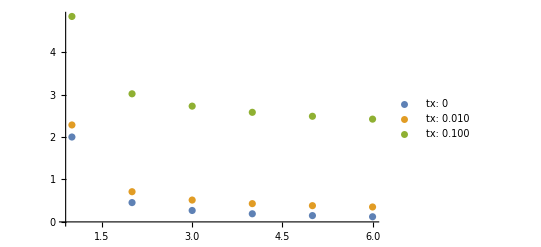

```mathematica
ListPlot[integratedTz, PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {3,3}]]&,  tzlist], PlotRange->All]
```

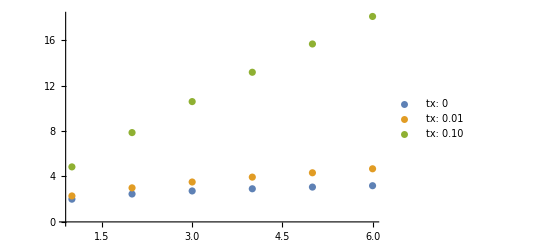

```mathematica
ListPlot[
Table[Accumulate[integratedTz[[i]]], {i, Length[tzlist]}], PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {2,2}]]&,  tzlist], PlotRange->All]
```

```mathematica
If[terms=={0,0,1},thirdTermContrib = integratedTz];
```

```mathematica
If[terms=={0,1},secondTermContrib = integratedTz];
```

```mathematica
If[terms=={1,0},firstTermContrib=integratedTz];
```

```mathematica
firstTermContrib/secondTermContrib //TableForm
```

1.9997/secondTermContrib | 0.454808/secondTermContrib | 0.268832/secondTermContrib | 0.191258/secondTermContrib | 0.148514/secondTermContrib | 0.121412/secondTermContrib
2.28373/secondTermContrib | 0.711117/secondTermContrib | 0.514677/secondTermContrib | 0.430307/secondTermContrib | 0.38251/secondTermContrib | 0.35138/secondTermContrib
4.84003/secondTermContrib | 3.0179/secondTermContrib | 2.72728/secondTermContrib | 2.58175/secondTermContrib | 2.48847/secondTermContrib | 2.4211/secondTermContrib

```mathematica
firstTermContrib +secondTermContrib //TableForm
```

1.9997+secondTermContrib | 0.454808+secondTermContrib | 0.268832+secondTermContrib | 0.191258+secondTermContrib | 0.148514+secondTermContrib | 0.121412+secondTermContrib
2.28373+secondTermContrib | 0.711117+secondTermContrib | 0.514677+secondTermContrib | 0.430307+secondTermContrib | 0.38251+secondTermContrib | 0.35138+secondTermContrib
4.84003+secondTermContrib | 3.0179+secondTermContrib | 2.72728+secondTermContrib | 2.58175+secondTermContrib | 2.48847+secondTermContrib | 2.4211+secondTermContrib

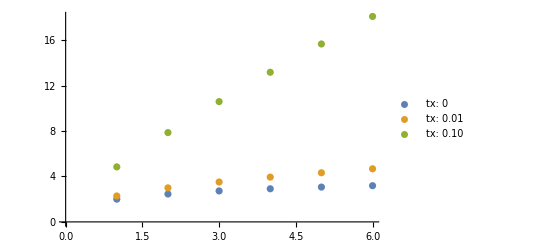

```mathematica
ListPlot[
Table[Accumulate[integratedTz[[i]]], {i, Length[tzlist]}], PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {2,2}]]&,  tzlist]]
```

```mathematica
Table[
integratedTz[[i]]-(integratedTz[[i]][[-1]]-integratedTz[[1]][[-1]]),
{i, Length[tzlist]}
]
```

{{1.9997,0.454808,0.268832,0.191258,0.148514,0.121412},{2.05376,0.481149,0.284708,0.200338,0.152541,0.121412},{2.54034,0.718216,0.427594,0.282061,0.188784,0.121412}}

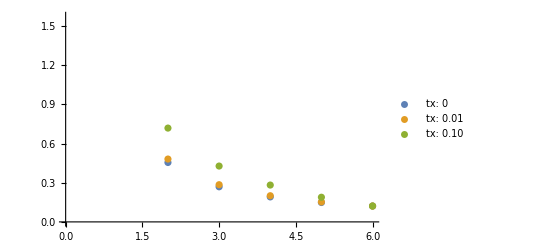

```mathematica
ListPlot[%, PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {2,2}]]&,  tzlist]]
```

## R & D mess

### Finding the anlytical contrib for tz>1

```mathematica
kernel[n]/.{m->0, n->1}
```

(2 (√(1+kappa^2)+kappa tz+kappa (-s+tz)) (HeavisideTheta[-kappa (-s+tz)]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((-kappa+√(1+kappa^2) s)^2 (1+1/((-kappa+√(1+kappa^2) s)^2)) (-√(1+kappa^2)-kappa tz+kappa (-s+tz)+ⅈ η)^2)

```mathematica
FullSimplify[%/.s->1, Assumptions->{{s, tz, kappa}∈Reals, s^2==1}]
```

((1+2 kappa (kappa+√(1+kappa^2)) tz) (HeavisideTheta[kappa-kappa tz]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/(√(1+kappa^2) (kappa+√(1+kappa^2)-ⅈ η)^2)

```mathematica
FullSimplify[%%/.s->-1, Assumptions->{{s, tz, kappa}∈Reals, s^2==1}]
```

((1+2 kappa (-kappa+√(1+kappa^2)) tz) (HeavisideTheta[-kappa (1+tz)]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/(√(1+kappa^2) (kappa-√(1+kappa^2)+ⅈ η)^2)

```mathematica
FullSimplify[%%%, Assumptions->{{s, tz, kappa}∈Reals, s^2==1}]
```

((√(1+kappa^2)-kappa s+2 kappa tz) (HeavisideTheta[kappa (s-tz)]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((1+kappa^2-kappa √(1+kappa^2) s) (√(1+kappa^2)+kappa s-ⅈ η)^2)

```mathematica
FullSimplify[
(kappa tz+kappa (tz)) (HeavisideTheta[-kappa (-s+tz)]-HeavisideTheta[-√(1+kappa^2)-kappa tz])/((-kappa+√(1+kappa^2) s)^2 (1+1/((-kappa+√(1+kappa^2) s)^2)) (-√(1+kappa^2)-kappa tz+kappa (-s+tz)+ⅈ η)^2),
Assumptions->{{s, tz, kappa}∈Reals, s^2==1}]
```

(kappa tz (HeavisideTheta[kappa (s-tz)]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((1+kappa^2-kappa √(1+kappa^2) s) (√(1+kappa^2)+kappa s-ⅈ η)^2)

```mathematica
%/.{{s->1},{s->-1, kappa->-kappa}}
```

{(kappa tz (HeavisideTheta[kappa (1-tz)]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((1+kappa^2-kappa √(1+kappa^2)) (kappa+√(1+kappa^2)-ⅈ η)^2),-(kappa tz (HeavisideTheta[-kappa (-1-tz)]-HeavisideTheta[-√(1+kappa^2)+kappa tz]))/((1+kappa^2-kappa √(1+kappa^2)) (kappa+√(1+kappa^2)-ⅈ η)^2)}

```mathematica
%//Simplify
```

{(kappa tz (HeavisideTheta[kappa-kappa tz]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((1+kappa^2-kappa √(1+kappa^2)) (kappa+√(1+kappa^2)-ⅈ η)^2),(kappa tz (HeavisideTheta[kappa+kappa tz]-HeavisideTheta[-√(1+kappa^2)+kappa tz]))/((-1-kappa^2+kappa √(1+kappa^2)) (kappa+√(1+kappa^2)-ⅈ η)^2)}

```mathematica
Integrate[(kappa tz)/((-1-kappa^2+kappa √(1+kappa^2)) (kappa+√(1+kappa^2)-ⅈ η)^2)/.η->0,
{kappa, 0, limit}, Assumptions->{{tz,s, η, limit}∈Reals, s^2==1,0<=tz<1, 0<=η<1, limit>0}]
```

-1/2 tz (limit (limit-√(1+limit^2))+ArcSinh[limit])

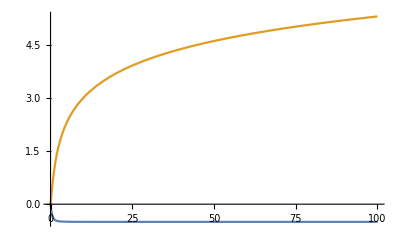

```mathematica
Plot[{limit (limit-√(1+limit^2)), ArcSinh[limit]}, {limit, 0,100}]
```

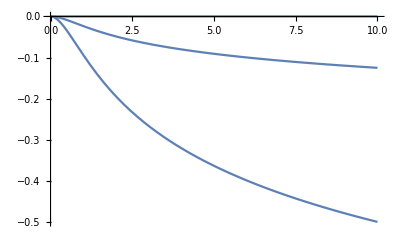

```mathematica
Plot[Table[-1/2 tz (limit (limit-√(1+limit^2))+ArcSinh[limit]), {tz,{0,0.1,0.4}}], {limit, 0,10}]
```

```mathematica
FullSimplify[Total[%/.{{s->1},{s->-1, kappa->-kappa}}], Assumptions->{{s, tz, kappa}∈Reals, s^2==1}]
```

((1+2 kappa (kappa+√(1+kappa^2)) tz) HeavisideTheta[kappa-kappa tz]-(1+2 kappa (kappa+√(1+kappa^2)) tz) HeavisideTheta[-√(1+kappa^2)-kappa tz]-(-1+2 kappa (kappa+√(1+kappa^2)) tz) (HeavisideTheta[kappa+kappa tz]-HeavisideTheta[-√(1+kappa^2)+kappa tz]))/(√(1+kappa^2) (kappa+√(1+kappa^2)-ⅈ η)^2)

```mathematica
((1+2 kappa (kappa+√(1+kappa^2)) tz) HeavisideTheta[kappa]-(-1+2 kappa (kappa+√(1+kappa^2)) tz) (HeavisideTheta[kappa]))/(√(1+kappa^2) (kappa+√(1+kappa^2)-ⅈ η)^2)
```

```mathematica
Integrate[
((1+2 kappa (kappa+√(1+kappa^2)) tz) HeavisideTheta[kappa]-(-1+2 kappa (kappa+√(1+kappa^2)) tz) (HeavisideTheta[kappa]))/(√(1+kappa^2) (kappa+√(1+kappa^2)-ⅈ η)^2),
{kappa, 0,Infinity},
Assumptions->{{tz,s, η, limit}∈Reals, s^2==1,0<=tz<1, 0<=η<1, limit>0}
]
```

(2 (η/(ⅈ+η)-Log[1-ⅈ η]))/η^2

```mathematica
Limit[%, η->0]
```

1

```mathematica
FullSimplify[((2 tz kappa s ) (HeavisideTheta[s (kappa-kappa tz)]-HeavisideTheta[-√(1+kappa^2)-kappa s tz]))/((1+kappa^2-kappa √(1+kappa^2) s) (√(1+kappa^2)+kappa s-ⅈ η)^2), , Assumptions->{{s, tz, kappa}∈Reals, s^2==1}]
```

(2 kappa s tz (HeavisideTheta[s (kappa-kappa tz)]-HeavisideTheta[-√(1+kappa^2)-kappa s tz]))/((1+kappa^2-kappa √(1+kappa^2) s) (√(1+kappa^2)+kappa s-ⅈ η)^2)

```mathematica
Integrate[
((2 tz kappa s ) (HeavisideTheta[s (kappa-kappa tz)]-HeavisideTheta[-√(1+kappa^2)-kappa s tz]))/((1+kappa^2-kappa √(1+kappa^2) s) (√(1+kappa^2)+kappa s-ⅈ η)^2)/.s->1,
{kappa, 0,Infinity},
Assumptions->{{tz,s, η, limit}∈Reals, s^2==1,0<=tz<1, 0<=η<1, limit>0}
]
```

Integrate::idiv: Integral of (2 kappa tz)/((1+kappa^2-kappa √(1+kappa^2)) (kappa+√(1+kappa^2)-ⅈ η)^2) does not converge on {0,∞}.

Integrate[(2 kappa tz (HeavisideTheta[kappa-kappa tz]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((1+kappa^2-kappa √(1+kappa^2)) (kappa+√(1+kappa^2)-ⅈ η)^2),{kappa,0,∞},Assumptions→{(tz|s|η|limit)∈ℝ,s^2==1,0≤tz<1,0≤η<1,limit>0}]

```mathematica
Limit[%, η->0]
```

1/2

```mathematica
Integrate[
((1+2 kappa (kappa+√(1+kappa^2)) tz) )/(√(1+kappa^2) (kappa+√(1+kappa^2)-ⅈ η)^2),
{kappa, 0, limit},
Assumptions->{{tz,s, η, limit}∈Reals, s^2==1,0<=tz<1, 0<=η<1, limit>0}
]
```

-ⅈ/(η (ⅈ+η) (ⅈ limit+ⅈ √(1+limit^2)+η))+(ⅈ limit)/(η (ⅈ+η) (ⅈ limit+ⅈ √(1+limit^2)+η))+(ⅈ √(1+limit^2))/(η (ⅈ+η) (ⅈ limit+ⅈ √(1+limit^2)+η))-(2 limit tz)/(1+2 ⅈ limit η+η^2)+(ⅈ tz)/(η (1+2 ⅈ limit η+η^2))+(ⅈ limit tz)/(η (1+2 ⅈ limit η+η^2))-(ⅈ √(1+limit^2) tz)/(η (1+2 ⅈ limit η+η^2))+(ⅈ tz η)/(1+2 ⅈ limit η+η^2)-(ⅈ limit tz η)/(1+2 ⅈ limit η+η^2)-(ⅈ √(1+limit^2) tz η)/(1+2 ⅈ limit η+η^2)+(ⅈ tz (3+η^4) ArcTan[(2 limit η)/(1+η^2)])/(4 η^4)+(ⅈ tz (-3-2 η^2+η^4) ArcTan[(2 limit η)/(1+η^2)])/(4 η^4)+(tz Log[32])/(2 η^2 (1+2 ⅈ limit η+η^2))+(ⅈ limit tz Log[32])/(η (1+2 ⅈ limit η+η^2))-(ⅈ limit tz η Log[32])/(1+2 ⅈ limit η+η^2)-(tz η^2 Log[32])/(2 (1+2 ⅈ limit η+η^2))-(tz (-3+η^4) Log[-limit+√(1+limit^2)])/(4 η^4)-(tz (3+2 η^2+η^4) Log[-limit+√(1+limit^2)])/(4 η^4)+((1-ⅈ η) (limit+√(1+limit^2)-ⅈ η) Log[limit+√(1+limit^2)])/(η^2 (ⅈ+η) (ⅈ limit+ⅈ √(1+limit^2)+η))+Log[limit+√(1+limit^2)-ⅈ η]/((ⅈ+η) (ⅈ limit+ⅈ √(1+limit^2)+η))-(limit Log[limit+√(1+limit^2)-ⅈ η])/(η^2 (ⅈ+η) (ⅈ limit+ⅈ √(1+limit^2)+η))-(√(1+limit^2) Log[limit+√(1+limit^2)-ⅈ η])/(η^2 (ⅈ+η) (ⅈ limit+ⅈ √(1+limit^2)+η))+(ⅈ Log[limit+√(1+limit^2)-ⅈ η])/(η (ⅈ+η) (ⅈ limit+ⅈ √(1+limit^2)+η))+(ⅈ limit Log[limit+√(1+limit^2)-ⅈ η])/(η (ⅈ+η) (ⅈ limit+ⅈ √(1+limit^2)+η))+(ⅈ √(1+limit^2) Log[limit+√(1+limit^2)-ⅈ η])/(η (ⅈ+η) (ⅈ limit+ⅈ √(1+limit^2)+η))+((1-ⅈ η) (limit+√(1+limit^2)-ⅈ η) Log[-ⅈ (ⅈ+η)])/(η^2 (ⅈ+η) (ⅈ limit+ⅈ √(1+limit^2)+η))+(tz Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)])/(4 (1+2 ⅈ limit η+η^2))+(3 tz Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)])/(4 η^4 (1+2 ⅈ limit η+η^2))+(3 ⅈ limit tz Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)])/(2 η^3 (1+2 ⅈ limit η+η^2))+(5 tz Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)])/(4 η^2 (1+2 ⅈ limit η+η^2))+(ⅈ limit tz Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)])/(η (1+2 ⅈ limit η+η^2))-(ⅈ limit tz η Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)])/(2 (1+2 ⅈ limit η+η^2))-(tz η^2 Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)])/(4 (1+2 ⅈ limit η+η^2))+(tz Log[1+η^2])/(2 η^2 (1+2 ⅈ limit η+η^2))+(ⅈ limit tz Log[1+η^2])/(η (1+2 ⅈ limit η+η^2))-(ⅈ limit tz η Log[1+η^2])/(1+2 ⅈ limit η+η^2)-(tz η^2 Log[1+η^2])/(2 (1+2 ⅈ limit η+η^2))-(tz Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ limit η+η^2))])/(4 (1+2 ⅈ limit η+η^2))-(3 tz Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ limit η+η^2))])/(4 η^4 (1+2 ⅈ limit η+η^2))-(3 ⅈ limit tz Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ limit η+η^2))])/(2 η^3 (1+2 ⅈ limit η+η^2))-(5 tz Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ limit η+η^2))])/(4 η^2 (1+2 ⅈ limit η+η^2))-(ⅈ limit tz Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ limit η+η^2))])/(η (1+2 ⅈ limit η+η^2))+(ⅈ limit tz η Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ limit η+η^2))])/(2 (1+2 ⅈ limit η+η^2))+(tz η^2 Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ limit η+η^2))])/(4 (1+2 ⅈ limit η+η^2))-(tz Log[(η^5 (ⅈ+η))/((-ⅈ+η) (-1+η^2)^2 (3+η^4))])/(4 (1+2 ⅈ limit η+η^2))-(3 tz Log[(η^5 (ⅈ+η))/((-ⅈ+η) (-1+η^2)^2 (3+η^4))])/(4 η^4 (1+2 ⅈ limit η+η^2))-(3 ⅈ limit tz Log[(η^5 (ⅈ+η))/((-ⅈ+η) (-1+η^2)^2 (3+η^4))])/(2 η^3 (1+2 ⅈ limit η+η^2))-(3 tz Log[(η^5 (ⅈ+η))/((-ⅈ+η) (-1+η^2)^2 (3+η^4))])/(4 η^2 (1+2 ⅈ limit η+η^2))-(ⅈ limit tz η Log[(η^5 (ⅈ+η))/((-ⅈ+η) (-1+η^2)^2 (3+η^4))])/(2 (1+2 ⅈ limit η+η^2))-(tz η^2 Log[(η^5 (ⅈ+η))/((-ⅈ+η) (-1+η^2)^2 (3+η^4))])/(4 (1+2 ⅈ limit η+η^2))+(tz Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-1+η^2)^2 (1+2 ⅈ limit η+η^2) (3+η^4))])/(4 (1+2 ⅈ limit η+η^2))+(3 tz Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-1+η^2)^2 (1+2 ⅈ limit η+η^2) (3+η^4))])/(4 η^4 (1+2 ⅈ limit η+η^2))+(3 ⅈ limit tz Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-1+η^2)^2 (1+2 ⅈ limit η+η^2) (3+η^4))])/(2 η^3 (1+2 ⅈ limit η+η^2))+(3 tz Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-1+η^2)^2 (1+2 ⅈ limit η+η^2) (3+η^4))])/(4 η^2 (1+2 ⅈ limit η+η^2))+(ⅈ limit tz η Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-1+η^2)^2 (1+2 ⅈ limit η+η^2) (3+η^4))])/(2 (1+2 ⅈ limit η+η^2))+(tz η^2 Log[-(32 η^5 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-1+η^2)^2 (1+2 ⅈ limit η+η^2) (3+η^4))])/(4 (1+2 ⅈ limit η+η^2))-(tz Log[1+2 η^2+4 limit^2 η^2+η^4])/(4 η^2 (1+2 ⅈ limit η+η^2))-(ⅈ limit tz Log[1+2 η^2+4 limit^2 η^2+η^4])/(2 η (1+2 ⅈ limit η+η^2))+(ⅈ limit tz η Log[1+2 η^2+4 limit^2 η^2+η^4])/(2 (1+2 ⅈ limit η+η^2))+(tz η^2 Log[1+2 η^2+4 limit^2 η^2+η^4])/(4 (1+2 ⅈ limit η+η^2))

```mathematica
Plot3D[
Re[%548]/.η->0.1,
{limit, 100,1000},
(*{η, -0.4,0.4}*)
{tz, 0,1}
]
```

-Graphics3D-

```mathematica
Plot3D[Re[(ⅈ (1-tz+√(-1+tz^2)) η+(ⅈ+η) (-ⅈ+ⅈ tz+√(-1+tz^2) η) Log[-1+ⅈ η]+(1-ⅈ η) (-1+tz-ⅈ √(-1+tz^2) η) Log[(1-tz+ⅈ √(-1+tz^2) η)/(-1+tz)])/(η^2 (ⅈ+η) (-ⅈ+ⅈ tz+√(-1+tz^2) η))],
{tz,1,2},{η,-0.4,0.4}
]
```

-Graphics3D-

```mathematica
FullSimplify[Re[(ⅈ (1-tz+√(-1+tz^2)) η+(ⅈ+η) (-ⅈ+ⅈ tz+√(-1+tz^2) η) Log[-1+ⅈ η]+(1-ⅈ η) (-1+tz-ⅈ √(-1+tz^2) η) Log[(1-tz+ⅈ √(-1+tz^2) η)/(-1+tz)])/(η^2 (ⅈ+η) (-ⅈ+ⅈ tz+√(-1+tz^2) η))],
Assumptions->{{tz, η}∈Reals, tz>1}]
```

Re[(-((1-tz+√(-1+tz^2)) η)/((ⅈ+η) (1-tz+ⅈ √(-1+tz^2) η))+Log[-1+tz]+Log[-1+ⅈ η]-Log[1-tz+ⅈ √(-1+tz^2) η])/η^2]

```mathematica
Simplify[ComplexExpand[Re[-((1-tz+√(-1+tz^2)) η)/((ⅈ+η) (1-tz+ⅈ √(-1+tz^2) η))]],Assumptions->{{tz, η}∈Reals, tz>1}]
```

(2 η^2)/((1+η^2) (-1+tz+η^2+tz η^2))

```mathematica
Integrate[
1/(√(1+kappa^2) (kappa-√(1+kappa^2)+ⅈ η)^2)/.η->0,
{kappa, 0,Sqrt[1/(tz^2-1)]},
Assumptions->{{tz,s, η, limit}∈Reals, s^2==1,tz>1, 0<=η<1}
]
```

1/(-1+tz)

```mathematica
Limit[1/4 ((2+3 tz)/(1+tz)^2+ArcCsch[√(-1+tz^2)]), tz->1, Direction->"FromBelow"]
```

∞

```mathematica
Integrate[
(1)/(√(1+kappa^2) (kappa+√(1+kappa^2)-ⅈ η)^2)/.η->0,
{kappa, 0, -Sqrt[1/(tz^2-1)], 0}
]
```

0

```mathematica
Integrate[
(1+2 kappa (kappa+√(1+kappa^2)) tz)/(√(1+kappa^2) (kappa+√(1+kappa^2)-ⅈ η)^2),
{kappa, 0, limit},
Assumptions->{{tz,s, η, limit}∈Reals, s^2==1, 0<=tz<1, 0<=η<1}
]
```

ConditionalExpression[-(-(2 ⅈ η (-1+tz+tz η^2))/(1+η^2)+((-1+η^2) (-1+tz+tz η^2))/(1+η^2)+(1+tz (-1+η^2)) Log[8]+(1+tz (-1+η^2)) Log[1+η^2]+(1+tz (-1+η^2)) Log[(η^3 (ⅈ+η))/((-ⅈ+η) (-1+η^2)^2 (1+tz (-1+η^2)))])/(2 η^2)+((2 (-1+η^2) (-1+tz+tz η^2))/(1+2 ⅈ limit η+η^2)+(4 √(1+limit^2) η (-1+tz+tz η^2))/(-2 limit η+ⅈ (1+η^2))+2 (-1+tz+tz η^2) ArcSinh[limit]+2 ⅈ (1+tz (-1+η^2)) ArcTan[(2 limit η)/(1+η^2)]+(1+tz (-1+η^2)) Log[1+(2+4 limit^2) η^2+η^4]+2 (1+tz (-1+η^2)) Log[-(8 η^3 (limit+√(1+limit^2)-2 ⅈ η+limit η^2-√(1+limit^2) η^2))/((-1+η^2)^2 (1+2 ⅈ limit η+η^2) (1+tz (-1+η^2)))])/(4 η^2), limit≠0]

```mathematica
Plot3D[
ReIm[%178]/.η->0.9,
{tz, 0,0.5},
(*{η,0,1},*)
{limit, 0,1000},
AxesLabel->Automatic
]
```

-Graphics3D-

```mathematica
Limit[ReIm[%178]/.tz->0.2, limit->10^8]
```

$Aborted

```mathematica
Integrate[
(1-kappa/(√(1+kappa^2))) (√(1+kappa^2)+kappa (-1+2 tz)),
{kappa, 0,limit},
Assumptions->{{tz,s}∈Reals, s^2==1, 0<=tz<1}
]
```

(limit^2-√(limit^2) √(1+limit^2)) (-1+tz)+(√(limit^2) tz ArcSinh[limit])/limit

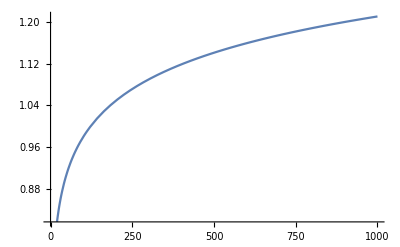

```mathematica
Plot[(limit^2-√(limit^2) √(1+limit^2)) (-1+tz)+(√(limit^2) tz ArcSinh[limit])/limit/.tz->0.1, {limit, 0,1000}]
```

```mathematica
NIntegrate[
((1-kappa/(√(1+kappa^2))) (kappa+√(1+kappa^2))^2 (√(1+kappa^2)+√(2+kappa^2)) )/((√(1+kappa^2)-√(2+kappa^2))^2 (2+kappa (kappa+√(2+kappa^2)))) ,
{kappa, -√(2/(-1+tz^2)),-√(1/(-1+tz^2))}
]/.tz->1.01
```

NIntegrate::nlim: kappa = -1.41421 √(1/(-1.+tz^2)) is not a valid limit of integration.

100.883

```mathematica
(1+s tz)/(s(tz^2-1))/.ssub/.tz->1.01
```

{100.,0.497512}

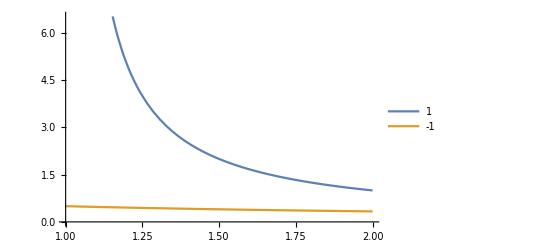

```mathematica
Plot[Evaluate[(1+s tz)/(s(tz^2-1))/.ssub], {tz, 1,2}, PlotLegends->(s/.ssub)]
```

```mathematica
Integrate[
(√(1+kappa^2)-kappa s+2 kappa tz)/(1+kappa^2+kappa √(1+kappa^2) s),
{kappa, -√(1/(-1+tz^2)),0},
Assumptions->{{tz,s}∈Reals, s^2==1, tz>1}
]
```

(-1+tz ArcCsch[√(-1+tz^2)])/s

```mathematica
Reduce[(s (kappa-kappa tz))(-√(1+kappa^2)-kappa s tz)<0,kappa]
```

(s<-1&&((tz<1/s&&-√(1/(-1+s^2 tz^2))<kappa<0)||(1/s≤tz≤-1/s&&kappa<0)||(-1/s<tz<1&&(kappa<0||kappa>√(1/(-1+s^2 tz^2))))||(tz>1&&0<kappa<√(1/(-1+s^2 tz^2)))))||(-1≤s<0&&((tz<1/s&&-√(1/(-1+s^2 tz^2))<kappa<0)||(1/s≤tz<1&&kappa<0)||(1<tz≤-1/s&&kappa>0)||(tz>-1/s&&0<kappa<√(1/(-1+s^2 tz^2)))))||(0<s≤1&&((tz<-1/s&&0<kappa<√(1/(-1+s^2 tz^2)))||(-1/s≤tz<1&&kappa>0)||(1<tz≤1/s&&kappa<0)||(tz>1/s&&-√(1/(-1+s^2 tz^2))<kappa<0)))||(s>1&&((tz<-1/s&&0<kappa<√(1/(-1+s^2 tz^2)))||(-1/s≤tz≤1/s&&kappa>0)||(1/s<tz<1&&(kappa<-√(1/(-1+s^2 tz^2))||kappa>0))||(tz>1&&-√(1/(-1+s^2 tz^2))<kappa<0)))

```mathematica
FullSimplify[(√(1+kappa^2)-kappa s+2 kappa tz)/(1+kappa^2+kappa √(1+kappa^2) s), Assumptions->{{kappa, s,tz}∈Reals, s^2==1}]
```

(√(1+kappa^2)-kappa s+2 kappa tz)/(1+kappa^2+kappa √(1+kappa^2) s)

```mathematica
Integrate[
(√(1+kappa^2)-kappa s+2 kappa tz)/(1+kappa^2+kappa √(1+kappa^2) s),
{kappa, -√(1/(-1+tz^2)),0},
Assumptions->{{tz,s}∈Reals, s^2==1, tz>1}
]
```

(-1+tz ArcCsch[√(-1+tz^2)])/s

```mathematica
Limit[(-1+tz ArcCsch[√(-1+tz^2)])/s/.s->1, tz->0]
```

-1

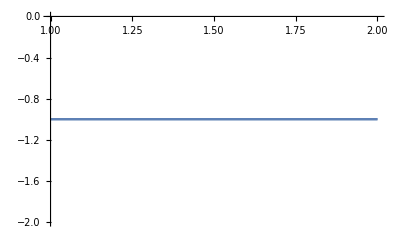

```mathematica
Plot[
%/.ssub,
{tz, 1,2}
]
```

```mathematica
kernel[n]/.{m->0,n->-1}
```

(2 (-√(1+kappa^2)-kappa tz+kappa (-s+tz)) (HeavisideTheta[-kappa (-s+tz)]-HeavisideTheta[√(1+kappa^2)-kappa tz]))/((-kappa-√(1+kappa^2) s)^2 (1+1/((-kappa-√(1+kappa^2) s)^2)) (√(1+kappa^2)-kappa tz+kappa (-s+tz))^2)

```mathematica
FullSimplify[%, Assumptions->{{s, tz, kappa}∈Reals, s^2==1}]
```

((√(1+kappa^2)+kappa s) (-HeavisideTheta[kappa (s-tz)]+HeavisideTheta[√(1+kappa^2)-kappa tz]))/(1+kappa^2-kappa √(1+kappa^2) s)

```mathematica
Reduce[(kappa (s-tz))(√(1+kappa^2)-kappa tz)<0,kappa]
```

(s<-1&&((tz<s&&-√(1/(-1+tz^2))<kappa<0)||(s<tz<-1&&(kappa<-√(1/(-1+tz^2))||kappa>0))||(-1≤tz≤1&&kappa>0)||(tz>1&&0<kappa<√(1/(-1+tz^2)))))||(-1≤s≤1&&((tz<-1&&-√(1/(-1+tz^2))<kappa<0)||(-1≤tz<s&&kappa<0)||(s<tz≤1&&kappa>0)||(tz>1&&0<kappa<√(1/(-1+tz^2)))))||(s>1&&((tz<-1&&-√(1/(-1+tz^2))<kappa<0)||(-1≤tz≤1&&kappa<0)||(1<tz<s&&(kappa<0||kappa>√(1/(-1+tz^2))))||(tz>s&&0<kappa<√(1/(-1+tz^2)))))

```mathematica
FullSimplify[(√(1+kappa^2)+kappa (s-2 tz))/(1+kappa^2-kappa √(1+kappa^2) s), Assumptions->{{kappa, s,tz}∈Reals, s^2==1}]
```

(√(1+kappa^2)+kappa s-2 kappa tz)/(1+kappa^2-kappa √(1+kappa^2) s)

```mathematica
Integrate[
(√(1+kappa^2)+kappa s-2 kappa tz)/(1+kappa^2-kappa √(1+kappa^2) s),
{kappa, 0,√(1/(-1+tz^2))},
Assumptions->{{tz,s}∈Reals, s^2==1, tz>1}
]
```

(-1+tz ArcCsch[√(-1+tz^2)])/s

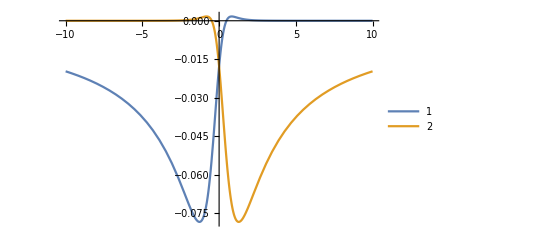

```mathematica
Plot[  Evaluate[(ϵ[m] + ϵ[n])alpha[n]^2 Sign[m](KroneckerDelta[n,0] HeavisideTheta[Sign[m] s kappa] + (1-KroneckerDelta[n,0]))/((ϵ[m]-ϵ[n]+I η)^2 * (alpha[m]^2+1) *(alpha[n]^2+1))/.{{m->1,n->-2, η->0, s->1},{m->-1,n->2, η->0, s->1}}/.tz->0.4],
{kappa, -10, 10},
PlotLegends->Automatic
]
```

### Other mess

```mathematica
xi kappa alpha[n]^2/.{m->0, n->1}/.HeavisideTheta[i_]-HeavisideTheta[j_]->1
```

(2 kappa)/((-kappa+√(1+kappa^2) s)^2 (1+1/((-kappa+√(1+kappa^2) s)^2)) (-√(1+kappa^2)-kappa s tz+kappa (-s+s tz)+ⅈ η)^2)

```mathematica
%/.s->1//Simplify
```

-kappa/((-1-kappa^2+kappa √(1+kappa^2)) (kappa+√(1+kappa^2)-ⅈ η)^2)

```mathematica
FullSimplify[%, Assumptions->{{kappa, tz}∈Reals}]
```

-(kappa (-1-kappa/(√(1+kappa^2))))/((kappa+√(1+kappa^2)-ⅈ η)^2)

```mathematica
Integrate[(kappa (-1-kappa/(√(1+kappa^2))))/((kappa+√(1+kappa^2)-ⅈ η)^2), {kappa, 0, L}, Assumptions->{L∈PositiveReals, η∈Reals, 0<=η<1}]
```

1/(8 η^4 (1+2 ⅈ L η+η^2))(-4 ⅈ η^3-4 ⅈ L η^3+4 ⅈ √(1+L^2) η^3+8 L η^4-4 ⅈ η^5+4 ⅈ L η^5+4 ⅈ √(1+L^2) η^5+2 η^2 (2 L η (-1+η^2)-ⅈ (-1+η^4)) ArcTan[(2 L η)/(1+η^2)]-3 Log[32]-6 ⅈ L η Log[32]-5 η^2 Log[32]-4 ⅈ L η^3 Log[32]-η^4 Log[32]+2 ⅈ L η^5 Log[32]+η^6 Log[32]+2 η^2 (1+η^2) (1+2 ⅈ L η+η^2) Log[-L+√(1+L^2)]-3 Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)]-6 ⅈ L η Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)]-5 η^2 Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)]-4 ⅈ L η^3 Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)]-η^4 Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)]+2 ⅈ L η^5 Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)]+η^6 Log[η^5/((-ⅈ+η)^2 (-3+η^2) (-1+η^2)^2)]-2 η^2 Log[1+η^2]-4 ⅈ L η^3 Log[1+η^2]+4 ⅈ L η^5 Log[1+η^2]+2 η^6 Log[1+η^2]-3 Log[-(L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2)/(1+2 ⅈ L η+η^2)]-6 ⅈ L η Log[-(L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2)/(1+2 ⅈ L η+η^2)]-3 η^2 Log[-(L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2)/(1+2 ⅈ L η+η^2)]-η^4 Log[-(L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2)/(1+2 ⅈ L η+η^2)]-2 ⅈ L η^5 Log[-(L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2)/(1+2 ⅈ L η+η^2)]-η^6 Log[-(L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2)/(1+2 ⅈ L η+η^2)]+3 Log[-(32 η^5 (L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ L η+η^2))]+6 ⅈ L η Log[-(32 η^5 (L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ L η+η^2))]+5 η^2 Log[-(32 η^5 (L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ L η+η^2))]+4 ⅈ L η^3 Log[-(32 η^5 (L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ L η+η^2))]+η^4 Log[-(32 η^5 (L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ L η+η^2))]-2 ⅈ L η^5 Log[-(32 η^5 (L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ L η+η^2))]-η^6 Log[-(32 η^5 (L+√(1+L^2)-2 ⅈ η+L η^2-√(1+L^2) η^2))/((-3+η^2) (-1+η^2)^2 (1+η^2) (1+2 ⅈ L η+η^2))]+3 Log[3+η^4]+6 ⅈ L η Log[3+η^4]+3 η^2 Log[3+η^4]+η^4 Log[3+η^4]+2 ⅈ L η^5 Log[3+η^4]+η^6 Log[3+η^4]+η^2 Log[1+(2+4 L^2) η^2+η^4]+2 ⅈ L η^3 Log[1+(2+4 L^2) η^2+η^4]-2 ⅈ L η^5 Log[1+(2+4 L^2) η^2+η^4]-η^6 Log[1+(2+4 L^2) η^2+η^4]+3 Log[(ⅈ+η)/(-3 ⅈ+3 η-ⅈ η^4+η^5)]+6 ⅈ L η Log[(ⅈ+η)/(-3 ⅈ+3 η-ⅈ η^4+η^5)]+3 η^2 Log[(ⅈ+η)/(-3 ⅈ+3 η-ⅈ η^4+η^5)]+η^4 Log[(ⅈ+η)/(-3 ⅈ+3 η-ⅈ η^4+η^5)]+2 ⅈ L η^5 Log[(ⅈ+η)/(-3 ⅈ+3 η-ⅈ η^4+η^5)]+η^6 Log[(ⅈ+η)/(-3 ⅈ+3 η-ⅈ η^4+η^5)])

```mathematica
Series[%%, {η, 0,1}, Assumptions->{η∈Reals, 0<=η<1}]
```

(3 (ⅈ π+5 Log[2]-Log[32]-Log[-L-√(1+L^2)]+Log[L+√(1+L^2)]))/(8 η^4)+1/(4 (L+√(1+L^2))^2 η^2)(5 Log[2]+10 L^2 Log[2]+10 L √(1+L^2) Log[2]-Log[32]-2 L^2 Log[32]-2 L √(1+L^2) Log[32]+Log[-L+√(1+L^2)]+2 L^2 Log[-L+√(1+L^2)]+2 L √(1+L^2) Log[-L+√(1+L^2)]+Log[L+√(1+L^2)]+2 L^2 Log[L+√(1+L^2)]+2 L √(1+L^2) Log[L+√(1+L^2)])+1/(8 (L+√(1+L^2))^4)(12 L^2+16 L^4+4 L √(1+L^2)+16 L^3 √(1+L^2)+ⅈ π+8 ⅈ L^2 π+8 ⅈ L^4 π+4 ⅈ L √(1+L^2) π+8 ⅈ L^3 √(1+L^2) π-5 Log[2]-40 L^2 Log[2]-40 L^4 Log[2]-20 L √(1+L^2) Log[2]-40 L^3 √(1+L^2) Log[2]+Log[32]+8 L^2 Log[32]+8 L^4 Log[32]+4 L √(1+L^2) Log[32]+8 L^3 √(1+L^2) Log[32]-Log[-L-√(1+L^2)]-8 L^2 Log[-L-√(1+L^2)]-8 L^4 Log[-L-√(1+L^2)]-4 L √(1+L^2) Log[-L-√(1+L^2)]-8 L^3 √(1+L^2) Log[-L-√(1+L^2)]+2 Log[-L+√(1+L^2)]+16 L^2 Log[-L+√(1+L^2)]+16 L^4 Log[-L+√(1+L^2)]+8 L √(1+L^2) Log[-L+√(1+L^2)]+16 L^3 √(1+L^2) Log[-L+√(1+L^2)]-Log[L+√(1+L^2)]-8 L^2 Log[L+√(1+L^2)]-8 L^4 Log[L+√(1+L^2)]-4 L √(1+L^2) Log[L+√(1+L^2)]-8 L^3 √(1+L^2) Log[L+√(1+L^2)])-(2 ⅈ (-1+5 L-11 L^2+20 L^3-12 L^4+16 L^5+√(1+L^2)-5 L √(1+L^2)+12 L^2 √(1+L^2)-12 L^3 √(1+L^2)+16 L^4 √(1+L^2)) η)/(3 (L+√(1+L^2))^5)+O[η]^2

```mathematica
Re[Normal[%129]]
```

2/3 Im[((-1+5 L-11 L^2+20 L^3-12 L^4+16 L^5+√(1+L^2)-5 L √(1+L^2)+12 L^2 √(1+L^2)-12 L^3 √(1+L^2)+16 L^4 √(1+L^2)) η)/((L+√(1+L^2))^5)]+Re[(3 (ⅈ π+5 Log[2]-Log[32]-Log[-L-√(1+L^2)]+Log[L+√(1+L^2)]))/(8 η^4)+1/(4 (L+√(1+L^2))^2 η^2)(5 Log[2]+10 L^2 Log[2]+10 L √(1+L^2) Log[2]-Log[32]-2 L^2 Log[32]-2 L √(1+L^2) Log[32]+Log[-L+√(1+L^2)]+2 L^2 Log[-L+√(1+L^2)]+2 L √(1+L^2) Log[-L+√(1+L^2)]+Log[L+√(1+L^2)]+2 L^2 Log[L+√(1+L^2)]+2 L √(1+L^2) Log[L+√(1+L^2)])+1/(8 (L+√(1+L^2))^4)(12 L^2+16 L^4+4 L √(1+L^2)+16 L^3 √(1+L^2)+ⅈ π+8 ⅈ L^2 π+8 ⅈ L^4 π+4 ⅈ L √(1+L^2) π+8 ⅈ L^3 √(1+L^2) π-5 Log[2]-40 L^2 Log[2]-40 L^4 Log[2]-20 L √(1+L^2) Log[2]-40 L^3 √(1+L^2) Log[2]+Log[32]+8 L^2 Log[32]+8 L^4 Log[32]+4 L √(1+L^2) Log[32]+8 L^3 √(1+L^2) Log[32]-Log[-L-√(1+L^2)]-8 L^2 Log[-L-√(1+L^2)]-8 L^4 Log[-L-√(1+L^2)]-4 L √(1+L^2) Log[-L-√(1+L^2)]-8 L^3 √(1+L^2) Log[-L-√(1+L^2)]+2 Log[-L+√(1+L^2)]+16 L^2 Log[-L+√(1+L^2)]+16 L^4 Log[-L+√(1+L^2)]+8 L √(1+L^2) Log[-L+√(1+L^2)]+16 L^3 √(1+L^2) Log[-L+√(1+L^2)]-Log[L+√(1+L^2)]-8 L^2 Log[L+√(1+L^2)]-8 L^4 Log[L+√(1+L^2)]-4 L √(1+L^2) Log[L+√(1+L^2)]-8 L^3 √(1+L^2) Log[L+√(1+L^2)])]

```mathematica
Plot3D[2/3 Im[((-1+5 L-11 L^2+20 L^3-12 L^4+16 L^5+√(1+L^2)-5 L √(1+L^2)+12 L^2 √(1+L^2)-12 L^3 √(1+L^2)+16 L^4 √(1+L^2)) η)/((L+√(1+L^2))^5)]+Re[(3 (ⅈ π+5 Log[2]-Log[32]-Log[-L-√(1+L^2)]+Log[L+√(1+L^2)]))/(8 η^4)+1/(4 (L+√(1+L^2))^2 η^2)(5 Log[2]+10 L^2 Log[2]+10 L √(1+L^2) Log[2]-Log[32]-2 L^2 Log[32]-2 L √(1+L^2) Log[32]+Log[-L+√(1+L^2)]+2 L^2 Log[-L+√(1+L^2)]+2 L √(1+L^2) Log[-L+√(1+L^2)]+Log[L+√(1+L^2)]+2 L^2 Log[L+√(1+L^2)]+2 L √(1+L^2) Log[L+√(1+L^2)])+1/(8 (L+√(1+L^2))^4)(12 L^2+16 L^4+4 L √(1+L^2)+16 L^3 √(1+L^2)+ⅈ π+8 ⅈ L^2 π+8 ⅈ L^4 π+4 ⅈ L √(1+L^2) π+8 ⅈ L^3 √(1+L^2) π-5 Log[2]-40 L^2 Log[2]-40 L^4 Log[2]-20 L √(1+L^2) Log[2]-40 L^3 √(1+L^2) Log[2]+Log[32]+8 L^2 Log[32]+8 L^4 Log[32]+4 L √(1+L^2) Log[32]+8 L^3 √(1+L^2) Log[32]-Log[-L-√(1+L^2)]-8 L^2 Log[-L-√(1+L^2)]-8 L^4 Log[-L-√(1+L^2)]-4 L √(1+L^2) Log[-L-√(1+L^2)]-8 L^3 √(1+L^2) Log[-L-√(1+L^2)]+2 Log[-L+√(1+L^2)]+16 L^2 Log[-L+√(1+L^2)]+16 L^4 Log[-L+√(1+L^2)]+8 L √(1+L^2) Log[-L+√(1+L^2)]+16 L^3 √(1+L^2) Log[-L+√(1+L^2)]-Log[L+√(1+L^2)]-8 L^2 Log[L+√(1+L^2)]-8 L^4 Log[L+√(1+L^2)]-4 L √(1+L^2) Log[L+√(1+L^2)]-8 L^3 √(1+L^2) Log[L+√(1+L^2)])], {L, 0,1000}, {η, 0,0.2}]
```

-Graphics3D-

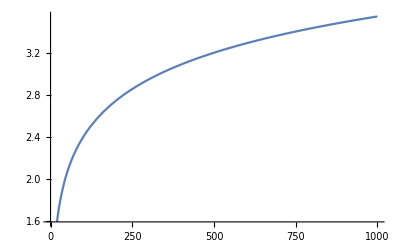

```mathematica
Plot[1/2 (L^2-L √(1+L^2)+ArcSinh[L]), {L, 0,1000}]
```

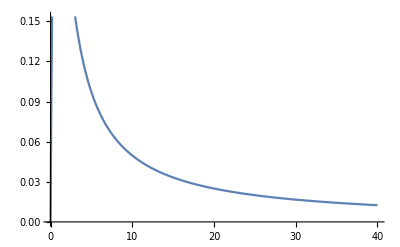

```mathematica
Plot[%, {kappa, 0,40}]
```

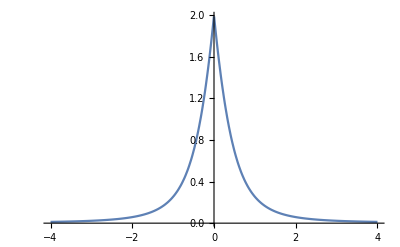

```mathematica
Plot[-(2 (-0.98 kappa-√(1+kappa^2)) HeavisideTheta[-kappa])/((-kappa-√(1+kappa^2))^2 ((0.+0.01 ⅈ)-1. kappa+√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)))+(2 (0.98 kappa+√(1+kappa^2)) HeavisideTheta[-kappa])/((-kappa-√(1+kappa^2))^2 ((0.+0.01 ⅈ)+1. kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)))+(2 (-0.98 kappa+√(1+kappa^2)) HeavisideTheta[kappa])/(((0.+0.01 ⅈ)-1. kappa-√(1+kappa^2))^2 (-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)))-(2 (0.98 kappa-√(1+kappa^2)) HeavisideTheta[kappa])/((-kappa+√(1+kappa^2))^2 ((0.+0.01 ⅈ)+1. kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2))),{kappa,-4,4}, PlotRange->All]
```

```mathematica
mntable[[1]]
```

(2 (√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[-kappa (-1+tz)]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[-kappa (-1+tz)]-HeavisideTheta[√(1+kappa^2)-kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa (1-tz)]-HeavisideTheta[-√(1+kappa^2)+kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa (1-tz)]-HeavisideTheta[√(1+kappa^2)+kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)

```mathematica
(2 (√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[kappa ]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[kappa ]-HeavisideTheta[√(1+kappa^2)-kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa ]-HeavisideTheta[-√(1+kappa^2)+kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa ]-HeavisideTheta[√(1+kappa^2)+kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)
```

(2 (√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[kappa]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[kappa]-HeavisideTheta[√(1+kappa^2)-kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa]-HeavisideTheta[-√(1+kappa^2)+kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa]-HeavisideTheta[√(1+kappa^2)+kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)

```mathematica
FullSimplify[(2 (√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[-kappa (-1+tz)]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[-kappa (-1+tz)]-HeavisideTheta[√(1+kappa^2)-kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa (1-tz)]-HeavisideTheta[-√(1+kappa^2)+kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa (1-tz)]-HeavisideTheta[√(1+kappa^2)+kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (1-tz)+kappa tz)^2),
Assumptions->{{kappa, tz} ∈Reals, 0<=tz<1}
]
```

-1/(1+kappa^2)(2 √(1+kappa^2) (-1+2 kappa^2 (-1+tz))+4 (kappa+kappa^3) (-1+tz) (HeavisideTheta[kappa (-1+tz)]-HeavisideTheta[kappa-kappa tz]))

```mathematica
NIntegrate[-1/(1+kappa^2)(2 √(1+kappa^2) (-1+2 kappa^2 (-1+tz))+4 (kappa+kappa^3) (-1+tz) (HeavisideTheta[kappa (-1+tz)]-HeavisideTheta[kappa-kappa tz]))/.tz->0.16, {kappa, -Infinity, Infinity}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-6.00789×10^14}. NIntegrate obtained 3.91737×10^18 and 3.91744×10^18 for the integral and error estimates.

3.91737×10^18

```mathematica
FullSimplify[mntableINTRA[[2]], Assumptions->{tz,kappa}∈Reals]
```

1/(2+3 kappa^2+kappa^4)(6+4 √(2+3 kappa^2+kappa^4)+3 kappa^2 (3+kappa^2+√(2+3 kappa^2+kappa^4))) ((√(1+kappa^2)+√(2+kappa^2)+2 kappa tz) HeavisideTheta[-√(1+kappa^2)-kappa tz]-(√(1+kappa^2)+√(2+kappa^2)-2 kappa tz) HeavisideTheta[√(1+kappa^2)-kappa tz]-√(1+kappa^2) HeavisideTheta[-√(2+kappa^2)-kappa tz]-√(2+kappa^2) HeavisideTheta[-√(2+kappa^2)-kappa tz]+√(1+kappa^2) HeavisideTheta[√(2+kappa^2)-kappa tz]+√(2+kappa^2) HeavisideTheta[√(2+kappa^2)-kappa tz]-2 kappa tz (HeavisideTheta[-√(2+kappa^2)-kappa tz]+HeavisideTheta[√(2+kappa^2)-kappa tz]))

```mathematica
(√(1+kappa^2)+√(2+kappa^2)+2 kappa tz) (HeavisideTheta[-√(1+kappa^2)-kappa tz]- HeavisideTheta[-√(2+kappa^2)-kappa tz])-(√(1+kappa^2)+√(2+kappa^2)-2 kappa tz)( HeavisideTheta[√(1+kappa^2)-kappa tz]+HeavisideTheta[√(2+kappa^2)-kappa tz])
```

```mathematica
Integrate[
((4+3 kappa^2+3 √(2+3 kappa^2+kappa^4)) (√(1+kappa^2)+√(2+kappa^2)-2 kappa tz))/(√(2+3 kappa^2+kappa^4)),
{kappa, 1/(√(-1+tz^2)),Sqrt[2]/(√(-1+tz^2))},Assumptions->{{kappa,tz}∈Reals,tz>1}
]
```

1/4 (-12 √2 √(1+tz^2)+12 √(-1+2 tz^2)-16 ArcSinh[1/(√2 √(-1+tz^2))]+16 ArcSinh[(√2)/(√(-1+tz^2))]-tz Log[1+3 tz^2-2 √2 tz √(1+tz^2)]+tz Log[1+3 tz^2+2 √2 tz √(1+tz^2)]+tz Log[-1+3 tz^2-2 tz √(-1+2 tz^2)]-tz Log[-1+3 tz^2+2 tz √(-1+2 tz^2)])

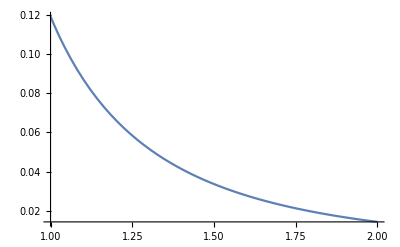

```mathematica
Plot[1/4 (-12 √2 √(1+tz^2)+12 √(-1+2 tz^2)-16 ArcSinh[1/(√2 √(-1+tz^2))]+16 ArcSinh[(√2)/(√(-1+tz^2))]-tz Log[1+3 tz^2-2 √2 tz √(1+tz^2)]+tz Log[1+3 tz^2+2 √2 tz √(1+tz^2)]+tz Log[-1+3 tz^2-2 tz √(-1+2 tz^2)]-tz Log[-1+3 tz^2+2 tz √(-1+2 tz^2)]), {tz, 1,2}]
```

```mathematica
FullSimplify[1/(2+3 kappa^2+kappa^4)(6+4 √(2+3 kappa^2+kappa^4)+3 kappa^2 (3+kappa^2+√(2+3 kappa^2+kappa^4))) (√(1+kappa^2)+√(2+kappa^2)-2 kappa tz), Assumptions->{kappa,tz}∈Reals]
```

((4+3 kappa^2+3 √(2+3 kappa^2+kappa^4)) (√(1+kappa^2)+√(2+kappa^2)-2 kappa tz))/(√(2+3 kappa^2+kappa^4))

```mathematica
Manipulate[
Plot[
{(HeavisideTheta[-√(1+kappa^2)-kappa tz]- HeavisideTheta[-√(2+kappa^2)-kappa tz]), -HeavisideTheta[√(1+kappa^2)-kappa tz]+HeavisideTheta[√(2+kappa^2)-kappa tz] },
{kappa,-4,4},PlotLegends->Automatic
],
{tz,0,2}]
```

```mathematica
Manipulate[
Plot[(√(1+kappa^2)+√(2+kappa^2)+2 kappa tz) HeavisideTheta[-√(1+kappa^2)-kappa tz]-(√(1+kappa^2)+√(2+kappa^2)-2 kappa tz) HeavisideTheta[√(1+kappa^2)-kappa tz]-√(1+kappa^2) HeavisideTheta[-√(2+kappa^2)-kappa tz]-√(2+kappa^2) HeavisideTheta[-√(2+kappa^2)-kappa tz]+√(1+kappa^2) HeavisideTheta[√(2+kappa^2)-kappa tz]+√(2+kappa^2) HeavisideTheta[√(2+kappa^2)-kappa tz]-2 kappa tz (HeavisideTheta[-√(2+kappa^2)-kappa tz]+HeavisideTheta[√(2+kappa^2)-kappa tz]), {kappa, -4,4}],
{tz, 0,2}]
```

```mathematica
(kernel[n]/.{m->1, n->2})/.s->-1
```

-((2 (2/((-kappa-√(1+kappa^2)) (-kappa-√(2+kappa^2))^2)+2/(-kappa-√(2+kappa^2))) (HeavisideTheta[-√(1+kappa^2)-kappa tz]-HeavisideTheta[-√(2+kappa^2)-kappa tz]))/((√(1+kappa^2)-√(2+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (1+2/((-kappa-√(2+kappa^2))^2))))

```mathematica
Reduce[(-√(1+kappa^2)-kappa tz)(-√(2+kappa^2)-kappa tz)<0]
```

(tz<-1&&√(1/(-1+tz^2))<kappa<√2 √(1/(-1+tz^2)))||(tz>1&&-√2 √(1/(-1+tz^2))<kappa<-√(1/(-1+tz^2)))

```mathematica
NIntegrate[
(4 (-kappa+√(2+kappa^2)+1/(-kappa+√(1+kappa^2))))/((kappa-√(2+kappa^2))^2 (√(1+kappa^2)-√(2+kappa^2))^2 (1+1/((kappa-√(1+kappa^2))^2)) (1+2/((kappa-√(2+kappa^2))^2))),
{kappa, -√2 √(1/(-1+tz^2)),-√(1/(-1+tz^2))}
]/.tz->1.1
```

NIntegrate::nlim: kappa = -1.41421 √(1/(-1.+tz^2)) is not a valid limit of integration.

20.3825

```mathematica
(kernel[n]/.{m->0, n->1})/.s->1
```

(2 (√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[-kappa (-1+tz)]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)

```mathematica
(kernel[n]/.{m->0, n->1})/.s->1
```

(2 (-√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[-kappa (-1+tz)]-HeavisideTheta[√(1+kappa^2)-kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)

```mathematica
NIntegrate[funcs[[1]], {kappa,-Infinity, Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-2.43643}. NIntegrate obtained 12.5116 and 0.01487 for the integral and error estimates.

12.5116

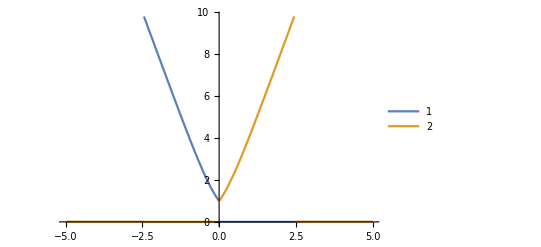

```mathematica
funcs={(kernel[n]/.{m->0, n->1}),(kernel[n]/.{m->0, n->-1})}/.{s->1,tz->1.08};
Plot[
funcs,
{kappa, -5,5},
PlotRange->All,
PlotLegends->Automatic
]
```

```mathematica
Manipulate[
Plot[mntableINTRA[[2]] +mntable[[2]]0/.tz->x, {kappa, -4,4}],
{x, -1.2,1.2}
]
```

```mathematica
(ϵ[m]-ϵ[n])/.ssub/.{m->-1, n->2}/.kappa->0//N
```

{-2.41421,-2.41421}

```mathematica
(ϵ[m]+ϵ[n])/.s->1/.{{m->1, n->2},{m->-1, n->-2, kappa->-kappa}}
```

{√(1+kappa^2)+√(2+kappa^2)+2 kappa tz,-√(1+kappa^2)-√(2+kappa^2)-2 kappa tz}

```mathematica
Manipulate[
Plot[ alpha[n]xi (ϵ[m]+ϵ[n])/.s->1/.{{m->1, n->2},{m->-1, n->-2}}/.tz->x, {kappa, -4,4}],
{x, -1.2,1.2}
]
```

```mathematica
s
```

```mathematica
xi (ϵ[m]+ϵ[n])alpha[n]^2 /.{{m->1, n->-2},{m->-1, n->2}}/.tz->0
```

{(4 (√(1+kappa^2)-√(2+kappa^2)) (HeavisideTheta[-√(1+kappa^2)]-HeavisideTheta[√(2+kappa^2)]))/((√(1+kappa^2)+√(2+kappa^2))^2 (-kappa-√(2+kappa^2) s)^2 (1+1/((-kappa+√(1+kappa^2) s)^2)) (1+2/((-kappa-√(2+kappa^2) s)^2))),(4 (-√(1+kappa^2)+√(2+kappa^2)) (HeavisideTheta[√(1+kappa^2)]-HeavisideTheta[-√(2+kappa^2)]))/((-√(1+kappa^2)-√(2+kappa^2))^2 (-kappa+√(2+kappa^2) s)^2 (1+1/((-kappa-√(1+kappa^2) s)^2)) (1+2/((-kappa+√(2+kappa^2) s)^2)))}

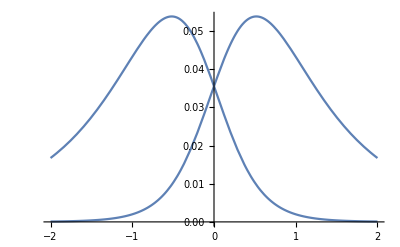

```mathematica
Plot[%955/.s->1, {kappa, -2, 2}]
```

```mathematica
xi (Sqrt[Abs[n]] alpha[n] + Sqrt[Abs[n]-1] alpha[m] alpha[n]^2)/.{{m->1, n->-2},{m->-1, n->2}}/.tz->0;
```

```mathematica
alpha[-2]
```

-(√2)/(-kappa-√(2+kappa^2) s)

```mathematica
xi/.{m->1,n->-2}
```

(2 (HeavisideTheta[-√(1+kappa^2)-kappa tz]-HeavisideTheta[√(2+kappa^2)-kappa tz]))/((√(1+kappa^2)+√(2+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2) s)^2)) (1+2/((-kappa-√(2+kappa^2) s)^2)))

```mathematica
Manipulate[
Plot[
Table[ϵ[n], {n, -4, 4}]/.s->y/.tz->x,
{kappa, -4, 4},
PlotRange->{-3,3}
],
{x, -1.2,1.2},
{y, -1,1,2}
]
```

```mathematica
Total[xi firstTerm[n]/.ssub]/.{m->1, n->-2}/.tz->0.8//Simplify
```

1/((√(1+kappa^2)+√(2+kappa^2))^2)4 (-((0.25 (kappa-1. √(1+kappa^2))^2 (-1.6 kappa-1. √(1+kappa^2)+√(2+kappa^2)) (HeavisideTheta[-0.8 kappa-1. √(1+kappa^2)]-1. HeavisideTheta[-0.8 kappa+√(2+kappa^2)]))/((1.+kappa^2-1. kappa √(1+kappa^2)) (2.+kappa^2+kappa √(2+kappa^2))))+(0.25 (kappa+√(1+kappa^2))^2 (-1.6 kappa+√(1+kappa^2)-1. √(2+kappa^2)) (HeavisideTheta[0.8 kappa-1. √(1+kappa^2)]-1. HeavisideTheta[0.8 kappa+√(2+kappa^2)]))/((1.+kappa^2+kappa √(1+kappa^2)) (2.+kappa^2-1. kappa √(2+kappa^2))))

```mathematica
Total[xi secondTerm/.ssub]/.{m->1, n->-2}/.tz->0.8//Simplify
```

1/((√(1+kappa^2)+√(2+kappa^2))^2)(-(((-kappa+√(1+kappa^2)) (-1-kappa^2+√(1+kappa^2) √(2+kappa^2)+kappa (√(1+kappa^2)-√(2+kappa^2))) (HeavisideTheta[-0.8 kappa-1. √(1+kappa^2)]-HeavisideTheta[-0.8 kappa+√(2+kappa^2)]))/((-1-kappa^2+kappa √(1+kappa^2)) (2+kappa^2+kappa √(2+kappa^2))))+((kappa+√(1+kappa^2)) (1+kappa^2-√(1+kappa^2) √(2+kappa^2)+kappa (√(1+kappa^2)-√(2+kappa^2))) (HeavisideTheta[0.8 kappa-1. √(1+kappa^2)]-HeavisideTheta[0.8 kappa+√(2+kappa^2)]))/((1+kappa^2+kappa √(1+kappa^2)) (2+kappa^2-kappa √(2+kappa^2))))

```mathematica
Total[xi secondTerm/.ssub]/.{m->-2, n->-3}/.tz->2//Simplify
```

1/((√(2+kappa^2)-√(3+kappa^2))^2)2 ((3 (kappa+√(2+kappa^2)) (2+kappa^2+√(2+kappa^2) √(3+kappa^2)+kappa (√(2+kappa^2)+√(3+kappa^2))) (HeavisideTheta[-2 kappa+√(2+kappa^2)]-HeavisideTheta[-2 kappa+√(3+kappa^2)]))/(4 (2+kappa^2+kappa √(2+kappa^2)) (3+kappa^2+kappa √(3+kappa^2)))+(3 (kappa-√(3+kappa^2)+2/(kappa-√(2+kappa^2))) (HeavisideTheta[2 kappa+√(2+kappa^2)]-HeavisideTheta[2 kappa+√(3+kappa^2)]))/((kappa-√(3+kappa^2))^2 (1+2/((kappa-√(2+kappa^2))^2)) (1+3/((kappa-√(3+kappa^2))^2))))

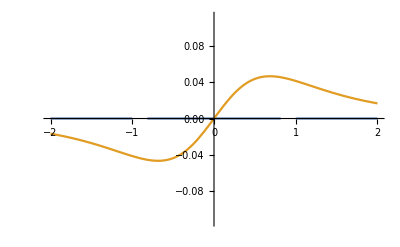

```mathematica
Plot[{%, %%}, {kappa, -2, 2}]
```

```mathematica
mntable=Table[
If[Abs[n]==Abs[m]+1,(xi firstTerm),0],
{m,-5,5}, {n,-10,10}
];
```

```mathematica
NIntegrate[mntable/.tz->0, {kappa, -Infinity, Infinity}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::inumr: The integrand (2 firstTerm (HeavisideTheta[√(5+kappa^2)]-HeavisideTheta[-√(6+Power[«2»])]))/((-√(5+kappa^2)-√(6+kappa^2))^2 (1+5/(-kappa-Power[«2»] s)^2) (1+6/(-kappa+Power[«2»] s)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::inumr: The integrand (2 firstTerm (HeavisideTheta[√(4+kappa^2)]-HeavisideTheta[-√(5+Power[«2»])]))/((-√(4+kappa^2)-√(5+kappa^2))^2 (1+4/(-kappa-Power[«2»] s)^2) (1+5/(-kappa+Power[«2»] s)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::inumr: The integrand (2 firstTerm (HeavisideTheta[√(3+kappa^2)]-HeavisideTheta[-√(4+Power[«2»])]))/((-√(3+kappa^2)-√(4+kappa^2))^2 (1+3/(-kappa-Power[«2»] s)^2) (1+4/(-kappa+Power[«2»] s)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[√(5+kappa^2)]-HeavisideTheta[-√(6+kappa^2)]))/((-√(5+kappa^2)-√(6+kappa^2))^2 (1+5/((-kappa-√(5+kappa^2) s)^2)) (1+6/((-kappa+√(6+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[√(4+kappa^2)]-HeavisideTheta[-√(5+kappa^2)]))/((-√(4+kappa^2)-√(5+kappa^2))^2 (1+4/((-kappa-√(4+kappa^2) s)^2)) (1+5/((-kappa+√(5+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[√(3+kappa^2)]-HeavisideTheta[-√(4+kappa^2)]))/((-√(3+kappa^2)-√(4+kappa^2))^2 (1+3/((-kappa-√(3+kappa^2) s)^2)) (1+4/((-kappa+√(4+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[√(2+kappa^2)]-HeavisideTheta[-√(3+kappa^2)]))/((-√(2+kappa^2)-√(3+kappa^2))^2 (1+2/((-kappa-√(2+kappa^2) s)^2)) (1+3/((-kappa+√(3+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[√(1+kappa^2)]-HeavisideTheta[-√(2+kappa^2)]))/((-√(1+kappa^2)-√(2+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2) s)^2)) (1+2/((-kappa+√(2+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (-HeavisideTheta[√(1+kappa^2)]+HeavisideTheta[kappa s]))/((√(1+kappa^2)-kappa s)^2 (1+1/((-kappa-√(1+kappa^2) s)^2))),{kappa,-∞,∞}],0.,NIntegrate[(2 firstTerm (-HeavisideTheta[-√(1+kappa^2)]+HeavisideTheta[kappa s]))/((-√(1+kappa^2)-kappa s)^2 (1+1/((-kappa+√(1+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[-√(1+kappa^2)]-HeavisideTheta[√(2+kappa^2)]))/((√(1+kappa^2)+√(2+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2) s)^2)) (1+2/((-kappa-√(2+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[-√(2+kappa^2)]-HeavisideTheta[√(3+kappa^2)]))/((√(2+kappa^2)+√(3+kappa^2))^2 (1+2/((-kappa+√(2+kappa^2) s)^2)) (1+3/((-kappa-√(3+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[-√(3+kappa^2)]-HeavisideTheta[√(4+kappa^2)]))/((√(3+kappa^2)+√(4+kappa^2))^2 (1+3/((-kappa+√(3+kappa^2) s)^2)) (1+4/((-kappa-√(4+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[-√(4+kappa^2)]-HeavisideTheta[√(5+kappa^2)]))/((√(4+kappa^2)+√(5+kappa^2))^2 (1+4/((-kappa+√(4+kappa^2) s)^2)) (1+5/((-kappa-√(5+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[-√(5+kappa^2)]-HeavisideTheta[√(6+kappa^2)]))/((√(5+kappa^2)+√(6+kappa^2))^2 (1+5/((-kappa+√(5+kappa^2) s)^2)) (1+6/((-kappa-√(6+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

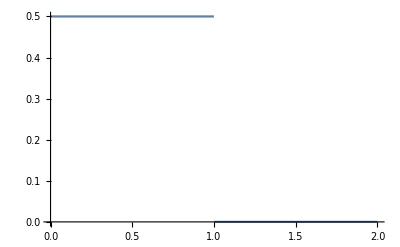

```mathematica
Plot[
Piecewise[{{1/2, tz<1}, {0, tz>1}}],
{tz,0,2}
]
```

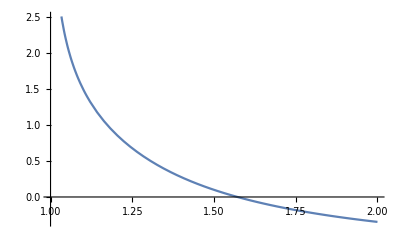

```mathematica
Plot[tz ArcCsch[tz^2-1]-1, {tz, 1,2}]
```